```mathematica
f = Function[t,Exp[-1/t]];
```

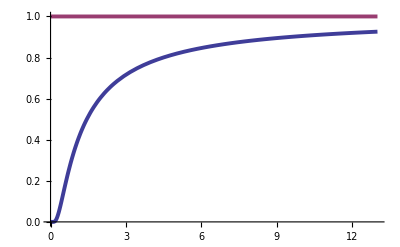

```mathematica
Plot[{f[t],1},{t,0.00001, 13}, PlotRange->All, PlotStyle->Thickness[0.007]]
```

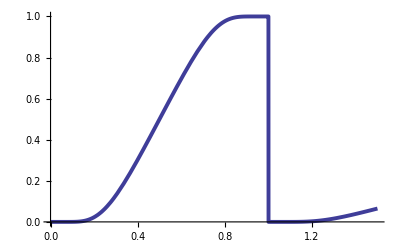

```mathematica
Plot[(f[t]/(f[t]+ f[1-t])),{t,0,1.5}, PlotRange->All, PlotStyle->Thickness[0.007]]
```